```mathematica
Ibias={3,3,5,5,2.5}
input[t_]:=1Sin[π t/400]HeavisideTheta[t-00.1]
Iinj [start_,dur_][t_]:=HeavisidePi[(t-start)/dur-1/2]
InputT[t_]:=3(Iinj[100,400][t])
InputT2[t_]:=3(Iinj[110,400][t])
zero[t_]:= 0
input1 = input
inputAnti[t_]:=1Sin[(π (t-400) /400)]HeavisideTheta[t-00.1]
inputAdv[t_]:=1Sin[(π (t-50) /400)]HeavisideTheta[t-00.1]
inputLag[t_]:=1Sin[(π (t+50) /400)]HeavisideTheta[t-00.1]
InpMat=
{
{input,input},
{input,inputAnti},
{input,inputAdv},
{input,inputLag}
};
InpMatT={
{InputT,InputT},
{zero,zero},
{InputT,InputT2},
{InputT2,InputT}
}

Inputs = Tuples[{InpMatT,InpMatT}]
Inputs = Flatten[#,1]&/@ Inputs
```

{3,3,5,5,2.5}

input

{{InputT,InputT},{zero,zero},{InputT,InputT2},{InputT2,InputT}}

{{{InputT,InputT},{InputT,InputT}},{{InputT,InputT},{zero,zero}},{{InputT,InputT},{InputT,InputT2}},{{InputT,InputT},{InputT2,InputT}},{{zero,zero},{InputT,InputT}},{{zero,zero},{zero,zero}},{{zero,zero},{InputT,InputT2}},{{zero,zero},{InputT2,InputT}},{{InputT,InputT2},{InputT,InputT}},{{InputT,InputT2},{zero,zero}},{{InputT,InputT2},{InputT,InputT2}},{{InputT,InputT2},{InputT2,InputT}},{{InputT2,InputT},{InputT,InputT}},{{InputT2,InputT},{zero,zero}},{{InputT2,InputT},{InputT,InputT2}},{{InputT2,InputT},{InputT2,InputT}}}

{{InputT,InputT,InputT,InputT},{InputT,InputT,zero,zero},{InputT,InputT,InputT,InputT2},{InputT,InputT,InputT2,InputT},{zero,zero,InputT,InputT},{zero,zero,zero,zero},{zero,zero,InputT,InputT2},{zero,zero,InputT2,InputT},{InputT,InputT2,InputT,InputT},{InputT,InputT2,zero,zero},{InputT,InputT2,InputT,InputT2},{InputT,InputT2,InputT2,InputT},{InputT2,InputT,InputT,InputT},{InputT2,InputT,zero,zero},{InputT2,InputT,InputT,InputT2},{InputT2,InputT,InputT2,InputT}}

```mathematica
gb=go
gin= 1.5
(*Ibias=
{0,1.5,2.5,2.5,2,
0,1.5,2.5,2.5,2,
3.25,3.25,3.1,3.1,-2.1} NIMP-NIMP->AND*)
Ibias = {0,1.5,2.5,2.5,2,
0,1.5,2.5,2.5,2,
3.6,3.6,3.3,3.3,-2.05}(*NIMP-NIMP-> NXOR *)
(*Ibias = {2,2,2.5,2.5,1.1-.5,
2,2,2.5,2.5,1.1-.5,
2,2,2.5,2.5,1.1-.5}+.5(*XOR-XOR-> XOR *)*)


Δt=1
Monitor[mydat=Reap[Do[
input1=sublists[[1]];
input2 = sublists[[2]];
input3 = sublists[[3]];
input4=sublists[[4]];
sol=NDSolve[
{(*neuron e1*)

Ve1x1'[t]==Fv[Ve1x1[t],We1x1[t]][Ibias[[1]],k,b]+input1[t]+gee Se2x1[t] +gie Si1x1[t]+Ibias[[1]],Ve1x1[0]==0,
We1x1'[t]==Fw[Ve1x1[t],We1x1[t]][a,b],We1x1[0]==6,
tau Se1x1'[t]== -Se1x1[t],Se1x1[0]==0,
WhenEvent[Ve1x1[t]==130,{Ve1x1[t]->c,We1x1[t]->We1x1[t]+d,Se1x1[t]->Se1x1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2x1'[t]==Fv[Ve2x1[t],We2x1[t]][Ibias[[2]],k,b]+input2[t]+gee Se1x1[t] +gie Si2x1[t]+Ibias[[2]],Ve2x1[0]==0,
We2x1'[t]==Fw[Ve2x1[t],We2x1[t]][a,b],We2x1[0]==6,
tau Se2x1'[t]== -Se2x1[t],Se2x1[0]==0,
WhenEvent[Ve2x1[t]==130,{Ve2x1[t]->c,We2x1[t]->We2x1[t]+d,Se2x1[t]->Se2x1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1x1'[t]==Fv[Vi1x1[t],Wi1x1[t]][Ibias[[3]],k,b]+input1[t]+gii Si2x1[t]+gei Se1x1[t]+Ibias[[3]],Vi1x1[0]==0,
Wi1x1'[t]==Fw[Vi1x1[t],Wi1x1[t]][a,b],Wi1x1[0]==6,
tau Si1x1'[t]== -Si1x1[t],Si1x1[0]==0,
WhenEvent[Vi1x1[t]==130,{Vi1x1[t]->c,Wi1x1[t]->Wi1x1[t]+d,Si1x1[t]->Si1x1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2x1'[t]==Fv[Vi2x1[t],Wi2x1[t]][Ibias[[4]],k,b]+input2[t]+gii Si1x1[t]+gei Se2x1[t]+Ibias[[4]],Vi2x1[0]==0,
Wi2x1'[t]==Fw[Vi2x1[t],Wi2x1[t]][a,b],Wi2x1[0]==6,
tau Si2x1'[t]== -Si2x1[t],Si2x1[0]==0,
WhenEvent[Vi2x1[t]==130,{Vi2x1[t]->c,Wi2x1[t]->Wi2x1[t]+d,Si2x1[t]->Si2x1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vox1'[t]==Fv[Vox1[t],Wox1[t]][Ibias[[5]],k,b]+go Se1x1[t]+go Se2x1[t],Vox1[0]==0,
Wox1'[t]==Fw[Vox1[t],Wox1[t]][a,b],Wox1[0]==6,
tau Sox1'[t]== -Sox1[t],Sox1[0]==0,
WhenEvent[Vox1[t]==130,{Vox1[t]->c,Wox1[t]->Wox1[t]+d,Sox1[t]->Sox1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],Vbx1'[t]==Fv[Vbx1[t],Wbx1[t]][Ibias[[5]],k,b]+gb Sox1[t],Vbx1[0]==0,
Wbx1'[t]==Fw[Vbx1[t],Wbx1[t]][a,b],Wbx1[0]==6,
tau Sbx1'[t]== -Sbx1[t],Sbx1[0]==0,
WhenEvent[Vbx1[t]==130,{Vbx1[t]->c,Wbx1[t]->Wbx1[t]+d,Sbx1[t]->Sbx1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e1*)
Ve1x2'[t]==Fv[Ve1x2[t],We1x2[t]][Ibias[[6]],k,b]+input3[t]+gee Se2x2[t] +gie Si1x2[t]+Ibias[[6]],Ve1x2[0]==0,
We1x2'[t]==Fw[Ve1x2[t],We1x2[t]][a,b],We1x2[0]==6,
tau Se1x2'[t]== -Se1x2[t],Se1x2[0]==0,
WhenEvent[Ve1x2[t]==130,{Ve1x2[t]->c,We1x2[t]->We1x2[t]+d,Se1x2[t]->Se1x2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2x2'[t]==Fv[Ve2x2[t],We2x2[t]][Ibias[[7]],k,b]+input4[t]+gee Se1x2[t] +gie Si2x2[t]+Ibias[[7]],Ve2x2[0]==0,
We2x2'[t]==Fw[Ve2x2[t],We2x2[t]][a,b],We2x2[0]==6,
tau Se2x2'[t]== -Se2x2[t],Se2x2[0]==0,
WhenEvent[Ve2x2[t]==130,{Ve2x2[t]->c,We2x2[t]->We2x2[t]+d,Se2x2[t]->Se2x2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1x2'[t]==Fv[Vi1x2[t],Wi1x2[t]][Ibias[[8]],k,b]+input3[t]+gii Si2x2[t]+gei Se1x2[t]+Ibias[[8]],Vi1x2[0]==0,
Wi1x2'[t]==Fw[Vi1x2[t],Wi1x2[t]][a,b],Wi1x2[0]==6,
tau Si1x2'[t]== -Si1x2[t],Si1x2[0]==0,
WhenEvent[Vi1x2[t]==130,{Vi1x2[t]->c,Wi1x2[t]->Wi1x2[t]+d,Si1x2[t]->Si1x2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2x2'[t]==Fv[Vi2x2[t],Wi2x2[t]][Ibias[[9]],k,b]+input4[t]+gii Si1x2[t]+gei Se2x2[t]+Ibias[[9]],Vi2x2[0]==0,
Wi2x2'[t]==Fw[Vi2x2[t],Wi2x2[t]][a,b],Wi2x2[0]==6,
tau Si2x2'[t]== -Si2x2[t],Si2x2[0]==0,
WhenEvent[Vi2x2[t]==130,{Vi2x2[t]->c,Wi2x2[t]->Wi2x2[t]+d,Si2x2[t]->Si2x2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vox2'[t]==Fv[Vox2[t],Wox2[t]][Ibias[[10]],k,b]+go Se1x2[t]+go Se2x2[t],Vox2[0]==0,
Wox2'[t]==Fw[Vox2[t],Wox2[t]][a,b],Wox2[0]==6,
tau Sox2'[t]== -Sox2[t],Sox2[0]==0,
WhenEvent[Vox2[t]==130,{Vox2[t]->c,Wox2[t]->Wox2[t]+d,Sox2[t]->Sox2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],Vbx2'[t]==Fv[Vbx2[t],Wbx2[t]][Ibias[[10]],k,b]+gb Sox2[t],Vbx2[0]==0,
Wbx2'[t]==Fw[Vbx2[t],Wbx2[t]][a,b],Wbx2[0]==6,
tau Sbx2'[t]== -Sbx2[t],Sbx2[0]==0,
WhenEvent[Vbx2[t]==130,{Vbx2[t]->c,Wbx2[t]->Wbx2[t]+d,Sbx2[t]->Sbx2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e1*)
Ve1x3'[t]==Fv[Ve1x3[t],We1x3[t]][Ibias[[11]],k,b]+Sbx1[t]+gee Se2x3[t] +gie Si1x3[t]+Ibias[[11]],Ve1x3[0]==0,
We1x3'[t]==Fw[Ve1x3[t],We1x3[t]][a,b],We1x3[0]==6,
tau Se1x3'[t]== -Se1x3[t],Se1x3[0]==0,
WhenEvent[Ve1x3[t]==130,{Ve1x3[t]->c,We1x3[t]->We1x3[t]+d,Se1x3[t]->Se1x3[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2x3'[t]==Fv[Ve2x3[t],We2x3[t]][Ibias[[12]],k,b]+Sbx2[t]+gee Se1x3[t] +gie Si2x3[t]+Ibias[[12]],Ve2x3[0]==0,
We2x3'[t]==Fw[Ve2x3[t],We2x3[t]][a,b],We2x3[0]==6,
tau Se2x3'[t]== -Se2x3[t],Se2x3[0]==0,
WhenEvent[Ve2x3[t]==130,{Ve2x3[t]->c,We2x3[t]->We2x3[t]+d,Se2x3[t]->Se2x3[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1x3'[t]==Fv[Vi1x3[t],Wi1x3[t]][Ibias[[13]],k,b]+Sbx1[t]+gii Si2x3[t]+gei Se1x3[t]+Ibias[[13]],Vi1x3[0]==0,
Wi1x3'[t]==Fw[Vi1x3[t],Wi1x3[t]][a,b],Wi1x3[0]==6,
tau Si1x3'[t]== -Si1x3[t],Si1x3[0]==0,
WhenEvent[Vi1x3[t]==130,{Vi1x3[t]->c,Wi1x3[t]->Wi1x3[t]+d,Si1x3[t]->Si1x3[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2x3'[t]==Fv[Vi2x3[t],Wi2x3[t]][Ibias[[14]],k,b]+Sbx2[t]+gii Si1x3[t]+gei Se2x3[t]+Ibias[[14]],Vi2x3[0]==0,
Wi2x3'[t]==Fw[Vi2x3[t],Wi2x3[t]][a,b],Wi2x3[0]==6,
tau Si2x3'[t]== -Si2x3[t],Si2x3[0]==0,
WhenEvent[Vi2x3[t]==130,{Vi2x3[t]->c,Wi2x3[t]->Wi2x3[t]+d,Si2x3[t]->Si2x3[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vox3'[t]==Fv[Vox3[t],Wox3[t]][Ibias[[15]],k,b]+go Se1x3[t]+go Se2x3[t],Vox3[0]==0,
Wox3'[t]==Fw[Vox3[t],Wox3[t]][a,b],Wox3[0]==6,
tau Sox3'[t]== -Sox3[t],Sox3[0]==0,
WhenEvent[Vox3[t]==130,{Vox3[t]->c,Wox3[t]->Wox3[t]+d,Sox3[t]->Sox3[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],Vbx3'[t]==Fv[Vbx3[t],Wbx3[t]][Ibias[[15]],k,b]+gb Sox3[t],Vbx3[0]==0,
Wbx3'[t]==Fw[Vbx3[t],Wbx3[t]][a,b],Wbx3[0]==6,
tau Sbx3'[t]== -Sbx3[t],Sbx3[0]==0,
WhenEvent[Vbx3[t]==130,{Vbx3[t]->c,Wbx3[t]->Wbx3[t]+d,Sbx3[t]->Sbx3[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1x1,We1x1,Se1x1,Ve2x1,We2x1,Se2x1,Vi1x1,Wi1x1,Si1x1,Vi2x1,Wi2x1,Si2x1,Vox1,Wox1,Sox1,Vbx1,Wbx1,Sbx1,
Ve1x2,We1x2,Se1x2,Ve2x2,We2x2,Se2x2,Vi1x2,Wi1x2,Si1x2,Vi2x2,Wi2x2,Si2x2,Vox2,Wox2,Sox2,Vbx2,Wbx2,Sbx2,
Ve1x3,We1x3,Se1x3,Ve2x3,We2x3,Se2x3,Vi1x3,Wi1x3,Si1x3,Vi2x3,Wi2x3,Si2x3,Vox3,Wox3,Sox3,Vbx3,Wbx3,Sbx3},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];
isSolve=False;
z=Sow[Table[tt= t;Sox3[t]/.sol[[1]],{t,0,time,Δt}]];
,{sublists,Inputs}]][[2,1]],{isSolve,tt}];
```

4

1.5

{0,1.5,2.5,2.5,2,0,1.5,2.5,2.5,2,3.6,3.6,3.3,3.3,-2.05}

1

```mathematica
|
```

```mathematica
Dimensions[mydat]
```

{16,1201}

{{InputT,InputT,InputT,InputT},{InputT,InputT,zero,zero},{InputT,InputT,InputT,InputT2},{InputT,InputT,InputT2,InputT},{zero,zero,InputT,InputT},{zero,zero,zero,zero},{zero,zero,InputT,InputT2},{zero,zero,InputT2,InputT},{InputT,InputT2,InputT,InputT},{InputT,InputT2,zero,zero},{InputT,InputT2,InputT,InputT2},{InputT,InputT2,InputT2,InputT},{InputT2,InputT,InputT,InputT},{InputT2,InputT,zero,zero},{InputT2,InputT,InputT,InputT2},{InputT2,InputT,InputT2,InputT}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

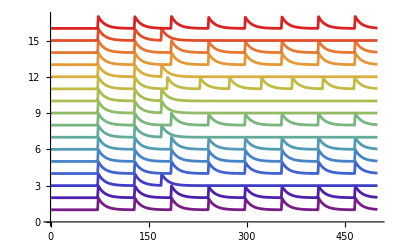

```mathematica
Inputs
range = Table[1*i,{i,16}]
colors=ColorData["Rainbow"][#]&/@Range[0,1,1/15];
ListLinePlot[mydat[[All,1;;500]]+range,PlotRange->All,PlotStyle->colors]
```